1.1 Exercise 1

```mathematica
data5=Import["C:\\Users\\JSTASTNY\\Downloads\Data1.txt","TSV"]
```

{{X,Y},{0.,3.4039},{0.5,3.9881},{1.,4.2004},{1.5,5.0291},{2.,5.188},{2.5,5.3914},{3.,5.7904},{3.5,5.4771},{4.,5.784},{4.5,5.9271},{5.,7.1422},{5.5,7.1213},{6.,6.8499},{6.5,7.936},{7.,8.3686},{7.5,8.2178},{8.,8.8891},{8.5,8.8176},{9.,8.8702},{9.5,9.8769},{10.,9.7354}}

```mathematica
data6=Rest[data5]
```

{{0.,3.4039},{0.5,3.9881},{1.,4.2004},{1.5,5.0291},{2.,5.188},{2.5,5.3914},{3.,5.7904},{3.5,5.4771},{4.,5.784},{4.5,5.9271},{5.,7.1422},{5.5,7.1213},{6.,6.8499},{6.5,7.936},{7.,8.3686},{7.5,8.2178},{8.,8.8891},{8.5,8.8176},{9.,8.8702},{9.5,9.8769},{10.,9.7354}}

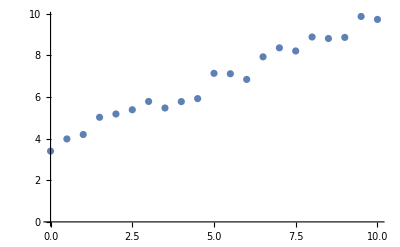

```mathematica
ListPlot[data6]
```

```mathematica
lsq=Fit[data6,{1,x},x]
```

3.6771+0.617003 x

```mathematica
ResLin=lmf["FitResiduals"]
```

{-0.273203,0.00249498,-0.0937066,0.426492,0.27689,0.171789,0.262287,-0.359514,-0.361116,-0.526517,0.380081,0.0506794,-0.529222,0.248376,0.372475,-0.0868268,0.275972,-0.10403,-0.359932,0.338267,-0.111735}

```mathematica
x=data6[[All,1]]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

```mathematica
y=Table[lsq,{x,0,10,0.5}]
```

{3.6771,3.98561,4.29411,4.60261,4.91111,5.21961,5.52811,5.83661,6.14512,6.45362,6.76212,7.07062,7.37912,7.68762,7.99613,8.30463,8.61313,8.92163,9.23013,9.53863,9.84713}

```mathematica
residuals=data6[[All,2]]-y
```

{-0.273203,0.00249498,-0.0937066,0.426492,0.27689,0.171789,0.262287,-0.359514,-0.361116,-0.526517,0.380081,0.0506794,-0.529222,0.248376,0.372475,-0.0868268,0.275972,-0.10403,-0.359932,0.338267,-0.111735}

```mathematica
z=Transpose[{x,residuals}]
```

{{0.,-0.273203},{0.5,0.00249498},{1.,-0.0937066},{1.5,0.426492},{2.,0.27689},{2.5,0.171789},{3.,0.262287},{3.5,-0.359514},{4.,-0.361116},{4.5,-0.526517},{5.,0.380081},{5.5,0.0506794},{6.,-0.529222},{6.5,0.248376},{7.,0.372475},{7.5,-0.0868268},{8.,0.275972},{8.5,-0.10403},{9.,-0.359932},{9.5,0.338267},{10.,-0.111735}}

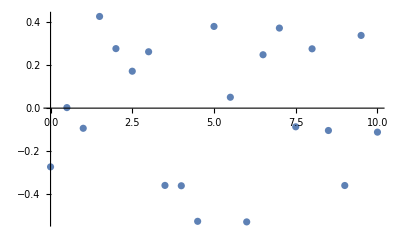

```mathematica
ListPlot[z]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
riffledata=Riffle[z,ErrorBar[0,0.3]]
```

{{0.,-0.273203},ErrorBar[0,0.3],{0.5,0.00249498},ErrorBar[0,0.3],{1.,-0.0937066},ErrorBar[0,0.3],{1.5,0.426492},ErrorBar[0,0.3],{2.,0.27689},ErrorBar[0,0.3],{2.5,0.171789},ErrorBar[0,0.3],{3.,0.262287},ErrorBar[0,0.3],{3.5,-0.359514},ErrorBar[0,0.3],{4.,-0.361116},ErrorBar[0,0.3],{4.5,-0.526517},ErrorBar[0,0.3],{5.,0.380081},ErrorBar[0,0.3],{5.5,0.0506794},ErrorBar[0,0.3],{6.,-0.529222},ErrorBar[0,0.3],{6.5,0.248376},ErrorBar[0,0.3],{7.,0.372475},ErrorBar[0,0.3],{7.5,-0.0868268},ErrorBar[0,0.3],{8.,0.275972},ErrorBar[0,0.3],{8.5,-0.10403},ErrorBar[0,0.3],{9.,-0.359932},ErrorBar[0,0.3],{9.5,0.338267},ErrorBar[0,0.3],{10.,-0.111735}}

```mathematica
partitiondata=Partition[riffledata,2]
```

{{{0.,-0.273203},ErrorBar[0,0.3]},{{0.5,0.00249498},ErrorBar[0,0.3]},{{1.,-0.0937066},ErrorBar[0,0.3]},{{1.5,0.426492},ErrorBar[0,0.3]},{{2.,0.27689},ErrorBar[0,0.3]},{{2.5,0.171789},ErrorBar[0,0.3]},{{3.,0.262287},ErrorBar[0,0.3]},{{3.5,-0.359514},ErrorBar[0,0.3]},{{4.,-0.361116},ErrorBar[0,0.3]},{{4.5,-0.526517},ErrorBar[0,0.3]},{{5.,0.380081},ErrorBar[0,0.3]},{{5.5,0.0506794},ErrorBar[0,0.3]},{{6.,-0.529222},ErrorBar[0,0.3]},{{6.5,0.248376},ErrorBar[0,0.3]},{{7.,0.372475},ErrorBar[0,0.3]},{{7.5,-0.0868268},ErrorBar[0,0.3]},{{8.,0.275972},ErrorBar[0,0.3]},{{8.5,-0.10403},ErrorBar[0,0.3]},{{9.,-0.359932},ErrorBar[0,0.3]},{{9.5,0.338267},ErrorBar[0,0.3]}}

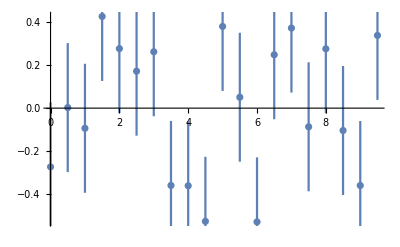

```mathematica
ErrorListPlot[partitiondata]
```

```mathematica
Lorentz=Import["C:\\Users\\JSTASTNY\\Downloads\\LorentzianData.txt","Table"]
```

{{-2.,0.26},{-1.9,0.69},{-1.8,0.4},{-1.7,0.86},{-1.6,0.72},{-1.5,0.54},{-1.4,0.52},{-1.3,0.68},{-1.2,0.96},{-1.1,0.73},{-1.,1.06},{-0.9,1.17},{-0.8,1.04},{-0.7,1.},{-0.6,1.19},{-0.5,1.65},{-0.4,1.34},{-0.3,1.9},{-0.2,1.75},{-0.1,1.64},{0.,1.72},{0.1,1.98},{0.2,1.75},{0.3,1.99},{0.4,2.19},{0.5,2.45},{0.6,2.28},{0.7,2.08},{0.8,2.1},{0.9,2.13},{1.,1.79},{1.1,1.7},{1.2,1.85},{1.3,1.9},{1.4,1.94},{1.5,1.72},{1.6,1.43},{1.7,1.23},{1.8,1.56},{1.9,1.16},{2.,1.25}}

```mathematica
Lfit=NonlinearModelFit[Lorentz,a/(1+((x-c)/w)^2),{{a,2.5},c,w},x]
```

FittedModel[2.16987/(1+0.467867 (-0.630755+x)^2)]

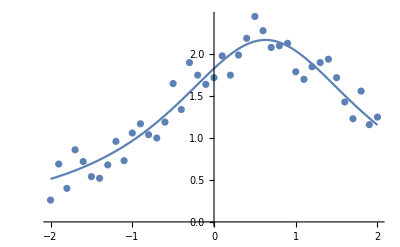

```mathematica
Show[ListPlot[Lorentz],Plot[Lfit[x],{x,-2,2}]]
```

```mathematica
nlfit=NonlinearModelFit[Lorentz,a/(1+((x-c)/w)^2),{{a,2.5},c,w},x]
```

FittedModel[2.16987/(1+0.467867 (-0.630755+x)^2)]

```mathematica
nlm = nlfit["BestFit"]
```

2.16987/(1+0.467867 (-0.630755+x)^2)

```mathematica
nlmtab=Table[nlm, {x,-2,2,.1}]
```

{0.511997,0.542934,0.576414,0.612671,0.651958,0.694541,0.740703,0.790733,0.84492,0.903546,0.966866,1.03509,1.10835,1.18666,1.26989,1.35768,1.44939,1.54404,1.64023,1.73611,1.82935,1.91718,1.99654,2.06421,2.11712,2.15265,2.16891,2.16501,2.14117,2.09869,2.03975,1.96721,1.88421,1.79394,1.69938,1.60314,1.50734,1.41368,1.32338,1.23729,1.15592}

```mathematica
ResLinResiduals=Lorentz[[All,2]]-nlmtab
```

{-0.251997,0.147066,-0.176414,0.247329,0.0680423,-0.154541,-0.220703,-0.110733,0.11508,-0.173546,0.0931344,0.134912,-0.0683461,-0.18666,-0.0798895,0.292321,-0.109392,0.355957,0.109765,-0.0961127,-0.109349,0.062815,-0.246542,-0.0742123,0.0728765,0.297352,0.111093,-0.0850102,-0.041172,0.0313143,-0.249751,-0.267205,-0.0342065,0.106058,0.240616,0.116865,-0.0773423,-0.183681,0.236618,-0.0772891,0.0940773}

```mathematica
ResLinErr=Riffle[ResLinResiduals,ErrorBar[0.3]]
```

{-0.251997,ErrorBar[0.3],0.147066,ErrorBar[0.3],-0.176414,ErrorBar[0.3],0.247329,ErrorBar[0.3],0.0680423,ErrorBar[0.3],-0.154541,ErrorBar[0.3],-0.220703,ErrorBar[0.3],-0.110733,ErrorBar[0.3],0.11508,ErrorBar[0.3],-0.173546,ErrorBar[0.3],0.0931344,ErrorBar[0.3],0.134912,ErrorBar[0.3],-0.0683461,ErrorBar[0.3],-0.18666,ErrorBar[0.3],-0.0798895,ErrorBar[0.3],0.292321,ErrorBar[0.3],-0.109392,ErrorBar[0.3],0.355957,ErrorBar[0.3],0.109765,ErrorBar[0.3],-0.0961127,ErrorBar[0.3],-0.109349,ErrorBar[0.3],0.062815,ErrorBar[0.3],-0.246542,ErrorBar[0.3],-0.0742123,ErrorBar[0.3],0.0728765,ErrorBar[0.3],0.297352,ErrorBar[0.3],0.111093,ErrorBar[0.3],-0.0850102,ErrorBar[0.3],-0.041172,ErrorBar[0.3],0.0313143,ErrorBar[0.3],-0.249751,ErrorBar[0.3],-0.267205,ErrorBar[0.3],-0.0342065,ErrorBar[0.3],0.106058,ErrorBar[0.3],0.240616,ErrorBar[0.3],0.116865,ErrorBar[0.3],-0.0773423,ErrorBar[0.3],-0.183681,ErrorBar[0.3],0.236618,ErrorBar[0.3],-0.0772891,ErrorBar[0.3],0.0940773}

```mathematica
x2 = Lorentz[[All,1]]
```

{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
z = Transpose[{x2,ResLinResiduals}]
```

{{-2.,-0.251997},{-1.9,0.147066},{-1.8,-0.176414},{-1.7,0.247329},{-1.6,0.0680423},{-1.5,-0.154541},{-1.4,-0.220703},{-1.3,-0.110733},{-1.2,0.11508},{-1.1,-0.173546},{-1.,0.0931344},{-0.9,0.134912},{-0.8,-0.0683461},{-0.7,-0.18666},{-0.6,-0.0798895},{-0.5,0.292321},{-0.4,-0.109392},{-0.3,0.355957},{-0.2,0.109765},{-0.1,-0.0961127},{0.,-0.109349},{0.1,0.062815},{0.2,-0.246542},{0.3,-0.0742123},{0.4,0.0728765},{0.5,0.297352},{0.6,0.111093},{0.7,-0.0850102},{0.8,-0.041172},{0.9,0.0313143},{1.,-0.249751},{1.1,-0.267205},{1.2,-0.0342065},{1.3,0.106058},{1.4,0.240616},{1.5,0.116865},{1.6,-0.0773423},{1.7,-0.183681},{1.8,0.236618},{1.9,-0.0772891},{2.,0.0940773}}

```mathematica
Clear[x]
```

```mathematica
nlfit=NonlinearModelFit[Lorentz,a/(1+((x-c)/w)^2),{{a,2.5},c,w},x]
```

FittedModel[2.16987/(1+0.467867 (-0.630755+x)^2)]

```mathematica
nl=Lorentz[[All,1]]
```

{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
nlm=Lfit["BestFit"]
```

2.16987/(1+0.467867 (-0.630755+x)^2)

```mathematica
nlmt=Table[nlm,{x,-2,2,0.1}]
```

{0.511997,0.542934,0.576414,0.612671,0.651958,0.694541,0.740703,0.790733,0.84492,0.903546,0.966866,1.03509,1.10835,1.18666,1.26989,1.35768,1.44939,1.54404,1.64023,1.73611,1.82935,1.91718,1.99654,2.06421,2.11712,2.15265,2.16891,2.16501,2.14117,2.09869,2.03975,1.96721,1.88421,1.79394,1.69938,1.60314,1.50734,1.41368,1.32338,1.23729,1.15592}

```mathematica
residuals1=Lorentz[[All,2]]-nlmt
```

{-0.251997,0.147066,-0.176414,0.247329,0.0680423,-0.154541,-0.220703,-0.110733,0.11508,-0.173546,0.0931344,0.134912,-0.0683461,-0.18666,-0.0798895,0.292321,-0.109392,0.355957,0.109765,-0.0961127,-0.109349,0.062815,-0.246542,-0.0742123,0.0728765,0.297352,0.111093,-0.0850102,-0.041172,0.0313143,-0.249751,-0.267205,-0.0342065,0.106058,0.240616,0.116865,-0.0773423,-0.183681,0.236618,-0.0772891,0.0940773}

```mathematica
z1=Transpose[{nl,residuals1}]
```

{{-2.,-0.251997},{-1.9,0.147066},{-1.8,-0.176414},{-1.7,0.247329},{-1.6,0.0680423},{-1.5,-0.154541},{-1.4,-0.220703},{-1.3,-0.110733},{-1.2,0.11508},{-1.1,-0.173546},{-1.,0.0931344},{-0.9,0.134912},{-0.8,-0.0683461},{-0.7,-0.18666},{-0.6,-0.0798895},{-0.5,0.292321},{-0.4,-0.109392},{-0.3,0.355957},{-0.2,0.109765},{-0.1,-0.0961127},{0.,-0.109349},{0.1,0.062815},{0.2,-0.246542},{0.3,-0.0742123},{0.4,0.0728765},{0.5,0.297352},{0.6,0.111093},{0.7,-0.0850102},{0.8,-0.041172},{0.9,0.0313143},{1.,-0.249751},{1.1,-0.267205},{1.2,-0.0342065},{1.3,0.106058},{1.4,0.240616},{1.5,0.116865},{1.6,-0.0773423},{1.7,-0.183681},{1.8,0.236618},{1.9,-0.0772891},{2.,0.0940773}}

```mathematica
riffledata1=Riffle[z1,ErrorBar[0,0.3]]
```

{{-2.,-0.251997},ErrorBar[0,0.3],{-1.9,0.147066},ErrorBar[0,0.3],{-1.8,-0.176414},ErrorBar[0,0.3],{-1.7,0.247329},ErrorBar[0,0.3],{-1.6,0.0680423},ErrorBar[0,0.3],{-1.5,-0.154541},ErrorBar[0,0.3],{-1.4,-0.220703},ErrorBar[0,0.3],{-1.3,-0.110733},ErrorBar[0,0.3],{-1.2,0.11508},ErrorBar[0,0.3],{-1.1,-0.173546},ErrorBar[0,0.3],{-1.,0.0931344},ErrorBar[0,0.3],{-0.9,0.134912},ErrorBar[0,0.3],{-0.8,-0.0683461},ErrorBar[0,0.3],{-0.7,-0.18666},ErrorBar[0,0.3],{-0.6,-0.0798895},ErrorBar[0,0.3],{-0.5,0.292321},ErrorBar[0,0.3],{-0.4,-0.109392},ErrorBar[0,0.3],{-0.3,0.355957},ErrorBar[0,0.3],{-0.2,0.109765},ErrorBar[0,0.3],{-0.1,-0.0961127},ErrorBar[0,0.3],{0.,-0.109349},ErrorBar[0,0.3],{0.1,0.062815},ErrorBar[0,0.3],{0.2,-0.246542},ErrorBar[0,0.3],{0.3,-0.0742123},ErrorBar[0,0.3],{0.4,0.0728765},ErrorBar[0,0.3],{0.5,0.297352},ErrorBar[0,0.3],{0.6,0.111093},ErrorBar[0,0.3],{0.7,-0.0850102},ErrorBar[0,0.3],{0.8,-0.041172},ErrorBar[0,0.3],{0.9,0.0313143},ErrorBar[0,0.3],{1.,-0.249751},ErrorBar[0,0.3],{1.1,-0.267205},ErrorBar[0,0.3],{1.2,-0.0342065},ErrorBar[0,0.3],{1.3,0.106058},ErrorBar[0,0.3],{1.4,0.240616},ErrorBar[0,0.3],{1.5,0.116865},ErrorBar[0,0.3],{1.6,-0.0773423},ErrorBar[0,0.3],{1.7,-0.183681},ErrorBar[0,0.3],{1.8,0.236618},ErrorBar[0,0.3],{1.9,-0.0772891},ErrorBar[0,0.3],{2.,0.0940773}}

```mathematica
partitiondata1=Partition[riffledata1,2]
```

{{{-2.,-0.251997},ErrorBar[0,0.3]},{{-1.9,0.147066},ErrorBar[0,0.3]},{{-1.8,-0.176414},ErrorBar[0,0.3]},{{-1.7,0.247329},ErrorBar[0,0.3]},{{-1.6,0.0680423},ErrorBar[0,0.3]},{{-1.5,-0.154541},ErrorBar[0,0.3]},{{-1.4,-0.220703},ErrorBar[0,0.3]},{{-1.3,-0.110733},ErrorBar[0,0.3]},{{-1.2,0.11508},ErrorBar[0,0.3]},{{-1.1,-0.173546},ErrorBar[0,0.3]},{{-1.,0.0931344},ErrorBar[0,0.3]},{{-0.9,0.134912},ErrorBar[0,0.3]},{{-0.8,-0.0683461},ErrorBar[0,0.3]},{{-0.7,-0.18666},ErrorBar[0,0.3]},{{-0.6,-0.0798895},ErrorBar[0,0.3]},{{-0.5,0.292321},ErrorBar[0,0.3]},{{-0.4,-0.109392},ErrorBar[0,0.3]},{{-0.3,0.355957},ErrorBar[0,0.3]},{{-0.2,0.109765},ErrorBar[0,0.3]},{{-0.1,-0.0961127},ErrorBar[0,0.3]},{{0.,-0.109349},ErrorBar[0,0.3]},{{0.1,0.062815},ErrorBar[0,0.3]},{{0.2,-0.246542},ErrorBar[0,0.3]},{{0.3,-0.0742123},ErrorBar[0,0.3]},{{0.4,0.0728765},ErrorBar[0,0.3]},{{0.5,0.297352},ErrorBar[0,0.3]},{{0.6,0.111093},ErrorBar[0,0.3]},{{0.7,-0.0850102},ErrorBar[0,0.3]},{{0.8,-0.041172},ErrorBar[0,0.3]},{{0.9,0.0313143},ErrorBar[0,0.3]},{{1.,-0.249751},ErrorBar[0,0.3]},{{1.1,-0.267205},ErrorBar[0,0.3]},{{1.2,-0.0342065},ErrorBar[0,0.3]},{{1.3,0.106058},ErrorBar[0,0.3]},{{1.4,0.240616},ErrorBar[0,0.3]},{{1.5,0.116865},ErrorBar[0,0.3]},{{1.6,-0.0773423},ErrorBar[0,0.3]},{{1.7,-0.183681},ErrorBar[0,0.3]},{{1.8,0.236618},ErrorBar[0,0.3]},{{1.9,-0.0772891},ErrorBar[0,0.3]}}

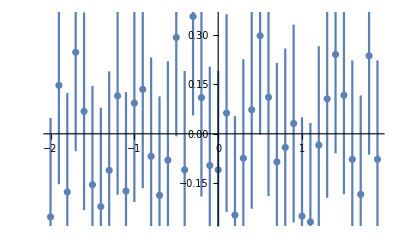

```mathematica
ErrorListPlot[partitiondata1]
```